runDM v1.0 - examples

With runDMC, It’s Tricky. With runDM, it’s not.

runDM is a tool for calculating the running of the couplings of Dark Matter (DM) to the Standard Model (SM) in simplified models with vector mediators. By specifying the mass of the mediator and the couplings of the mediator to SM fields at high energy, the code can be used to calculate the couplings at low energy, taking into account the mixing of all dimension-6 operators. The code can also be used to extract the operator coefficients relevant for direct detection, namely low energy couplings to up, down and strange quarks and to protons and neutrons. See the manual and arXiv:1605.XXXXX for more details.

Initialisation

Let’s start by loading in the runDM code.

```mathematica
Get[NotebookDirectory[] <> "runDM.m"];
```

First, let’s specify the couplings at high energy. This will be a 1-D array with 16 elements, defined in Eq. 4 of the manual. runDM comes with a number of pre-defined benchmarks, which can be accessed using setBenchmark.

```mathematica
chigh = setBenchmark["UniversalAxial"];
Print["Axial-vector coupling to all SM fermions: " <> ToString[chigh] ];

chigh = setBenchmark["LeptonsVector"];
Print["Vector coupling to all SM leptons: " <> ToString[chigh]];
```

Axial-vector coupling to all SM fermions: {-1., 1., 1., -1., 1., -1., 1., 1., -1., 1., -1., 1., 1., -1., 1., 0.}

Vector coupling to all SM leptons: {0., 0., 0., 1., 1., 0., 0., 0., 1., 1., 0., 0., 0., 1., 1., 0.}

Alternatively, you can specify each coupling individually. You can use initCouplings[] to generate an empty array of couplings and then go ahead. But any array of 16 elements will do.

```mathematica
chigh = initCouplings[];
chigh[[3]] = 1.0;
chigh[[7]] = -1.0;
Print["User-defined couplings: " <> ToString[chigh]];
```

User-defined couplings: {0, 0, 1., 0, 0, 0, -1., 0, 0, 0, 0, 0, 0, 0, 0, 0}

runCouplings: running between arbitrary scales

From these high energy couplings (defined at some energy E_1), you can obtain the couplings at a different energy scale E_2 by using runCouplings[c, E_1, E_2]. 

The input coupling vector c should always be the list of high energy couplings to fully gauge-invariant operators above the EW scale (see Eq. 4 of the manual) - even if E_1 is below m_Z. The output is either a list of coefficients for the same operators - if E_2 is above m_Z - or the list of coefficients for the low energy operators below the EW scale (Eq. 6 of the manual) - if E_2 is below m_Z. Don’t worry, runDM takes care of the relative values of E_1 and E_2.

```mathematica
(*Run from 1 TeV to 10 GeV*)
Subscript[E, 1] = 1000;Subscript[E, 2] = 10;
clow = runCouplings[chigh, Subscript[E, 1], Subscript[E, 2]]
```

{0.00747328,0.496264,-0.492527,-0.00373596,-0.00373619,-0.0112106,-0.0112106,-0.0112106,1.36429×10^-6,0.499999,-0.499999,-1.36429×10^-6,-1.12974×10^-6,-1.36429×10^-6,-1.36429×10^-6,-1.36129×10^-6}

DDCouplingsQuarks: calculating low-energy DM-quark couplings

If we’re only interested in direct detection experiments, we can use the function DDCouplingsQuarks[c, E_1] to extract the couplings to light quarks. In this case, the code evolves the couplings from energy E_1, down to the nuclear energy scale ~ 1 GeV. The output is an array with 5 elements, the vector and axial-vector couplings to light quarks: c_q=(c_V^(u),c_V^(d),c_A^(u),c_A^(d),c_A^(s)). Let’s calculate them and print them out.

```mathematica
(*Run from 10 TeV to 1 GeV*)
Subscript[E, 1]= 10000;
cq = DDCouplingsQuarks[chigh, Subscript[E, 1]];

clabels = {"c_V","c_V", "c_A", "c_A", "c_A"};
Grid[Transpose[{clabels, cq}]]
```

c_V | 0.0145847
c_V | 0.492712
c_A | 8.56843×10^-6
c_A | 0.499991
c_A | -8.56843×10^-6

Now, let’s take a look at the value of the low-energy light quark couplings (evaluated at μ_N ~ 1 GeV) as a function of the mediator mass m_V.

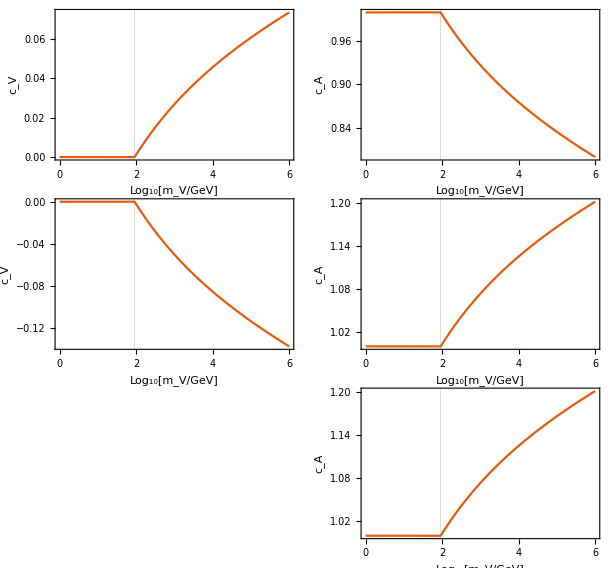

```mathematica
(*Set value of high energy couplings*)
chigh = setBenchmark["QuarksAxial"];

(*Calculate and plot low energy couplings*)
plots = Table[Plot[{DDCouplingsQuarks[chigh,10^Subscript[lm, V]][[k]]}, {Subscript[lm, V], 0.0, 6.0}, PlotTheme->"Scientific", FrameLabel->{"Log_10[m_V/GeV]", clabels[[k]]}, PlotRangePadding->.1,ImageSize->300, GridLines->{{Log10[91.1875]},{}}, BaseStyle->{FontSize->16}], {k,5}];

GraphicsGrid[{{plots[[1]], plots[[3]]},{ plots[[2]],plots[[4]]}, {,plots[[5]]}}, Spacings->0.0]
```

#### DDCouplingsNR: calculating low energy non-relativistic DM-nucleon couplings

The function DDCouplingsNR[c, E1, mx, DMcurrent, N] calculates the running of the operators to the nuclear energy scale, but it also performs the embedding of the quarks in the nucleon (N = ‘p’, ‘n’) and the matching onto the non-relativisitic (NR) DM-nucleon operators, defined in arXiv:1203.3542. In order to perform the matching, the user must specify mx (DM mass in GeV) and DMcurrent, the DM interaction structure. The meanings of the possible interactions structures (“scalar”, “vector” and “axial-vector”) are given in Eq. 8 of the manual.

The output is a list of coefficients of the first 12 NR operators, with numbering matching that of arXiv:1203.3542:

```mathematica
(*Set high energy couplings*)
chigh = setBenchmark["QuarksAxial"];

(*Set DM parameters*)
E1 = 10000; mx = 100; DMcurrent = "vector";
Print["NR DM-proton couplings: " <> ToString[DDCouplingsNR[chigh, E1, mx, DMcurrent, "p"], StandardForm]];
Print["NR DM-neutron couplings: " <> ToString[DDCouplingsNR[chigh, E1, mx, DMcurrent, "n"], StandardForm]];
```

NR DM-proton couplings: {2.29596×10^-8,0,0,0,0,0,-1.54825×10^-6,0,1.54825×10^-8,0,0,0}

NR DM-neutron couplings: {-4.68791×10^-7,0,0,0,0,0,-3.94846×10^-6,0,3.94846×10^-8,0,0,0}